# ЛР3. Анимация и динамическая интерактивность - 2.

## Динамическая интерактивность курсора мыши. Локатор.

```mathematica
Manipulate[{Graphics[{White,PointSize@0.01,Point[a]},PlotRange->{{0,10},{0,10}}],a},{a,Locator}]
```

### Задание 1.

Используя локатор, смоделируйте стрельбу пользователя по мишени (нажатием курсора мыши) с выводом количества очков при попадании. В центр - 10, дальше - 9 и т.д...

### Решение.

```mathematica
getHit[a_]:=If[a[[1]]==-10 &&a[[2]]==-10,"Shoot!",If[Norm[a]<=1,"10",If[1<Norm[a]<=2,"9",If[2<Norm[a]<=3,"8",If[3<Norm[a]<=4,"7",If[4<Norm[a]<=5,"6",If[5<Norm[a]<=6,"5",If[6<Norm[a]<=7,"4",If[7<Norm[a]<=8,"3",If[8<Norm[a]<=9,"2",If[9<Norm[a]<=10,"1",If[10<Norm[a],"Miss"]]]]]]]]]]]]
Manipulate[Graphics[{{Hue[#*0.1,0.8,1],Circle[{0,0},#]}&/@Range[1,10],Point[a],Text[Style[getHit[a],Blue,Bold,Italic,24],{8,9}]},PlotRange->{{-10,10.1},{-10.1,10}},ImageSize->Medium],{{a,{-10,-10}},Locator}]
```

```mathematica
{1,1}[[2]]
```

1

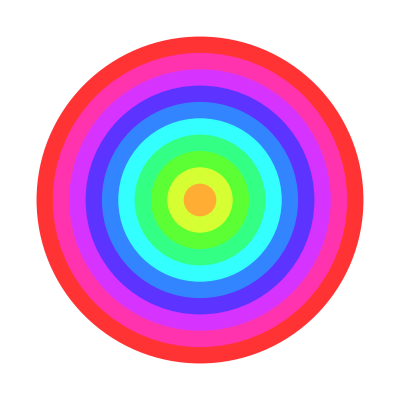

```mathematica
Graphics[{Hue[#*0.1,0.8,1],Disk[{0,0},#]}&/@Range[10,1,-1]]
```

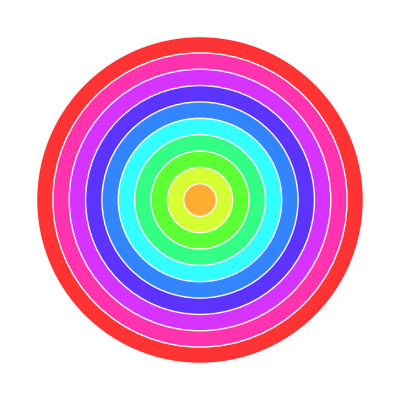

```mathematica
Graphics[{Hue[#*0.1,0.8,1],Disk[{0,0},#],White,Circle[{0,0},#]}&/@Range[10,1,-1]]
```

### Задание 2.

```mathematica
DynamicModule[{pts = {{0, 0}, {1, 1}, {2, 0}, {3, 2}}}, 
 LocatorPane[Dynamic[pts], 
  Dynamic[Plot[InterpolatingPolynomial[pts, x], {x, 0, 3}, 
    PlotRange -> 3]]]]
```

Задавая локатором набор из n точек задайте и отобразите интерполяционный полином для заданного набора точек. Количество точек задавайте с помощью функции Manipulate.

## Динамическая интерактивность курсора мыши. Click Pane.

### Пример - заготовка.

```mathematica
DynamicModule[{pointlist={},a=True},Column[{Button["Refresh",pointlist={}],Button["Action",a=Not[a]],Checkbox[Dynamic@a],ClickPane[Framed@Dynamic@Graphics[{PointSize@0.02,Point/@pointlist,If[a,Line[pointlist]]},PlotRange->{{0,10},{0,10}},ImageSize->500],AppendTo[pointlist,#]&]}]]
```

### Задание 3.

Приведите графический интерфейс пользователя, позволяющий изобразить произвольное число точек. Координаты точек, пользователь задаёт курсором мыши. Подсветите красным две самых далёких точки множества, а зелёным две самых близких.  Выведите текстом количество точек, минимальное и максимальное расстояние на графическую область. Предусмотрите кнопку для сброса набора точек и удаления последней точки.  Ближайшие и наиболее отдалённые точки отыщите методом перебора, используя функцию DistanceMatrix.

```mathematica
pts = RandomReal[{0,10},{10,2}]
```

```mathematica
DistanceMatrix[pts]
```

### Задание 4.

Приведите графический интерфейс пользователя позволяющий изобразить треугольник и вписанную в него окружность . Координаты точек, пользователь задаёт курсором мыши .